```mathematica
secondnet= net[1, 1,10,2]
```

NetChain[<>]

```mathematica
data=Table[{x,oscillator[2,20,x]},{x,0,0.5,0.05}];
traindata =Table[{data[[i]][[1]]}-> {data[[i]][[2]]}, {i, 1, Length[data]}];
traindata = RandomChoice[traindata, Length[traindata]]
```

{{0.15}→{-0.722897},{0.25}→{0.113595},{0.3}→{0.511541},{0.5}→{-0.328791},{0.1}→{-0.26589},{0.2}→{-0.489136},{0.}→{1.},{0.45}→{-0.353598},{0.35}→{0.407166},{0.5}→{-0.328791},{0.05}→{0.565409}}

```mathematica
xData= #[[1]]&/@traindata
```

{{0.15},{0.25},{0.3},{0.5},{0.1},{0.2},{0.},{0.45},{0.35},{0.5},{0.05}}

```mathematica
Targets = #[[2]]&/@traindata
```

{{-0.722897},{0.113595},{0.511541},{-0.328791},{-0.26589},{-0.489136},{1.},{-0.353598},{0.407166},{-0.328791},{0.565409}}

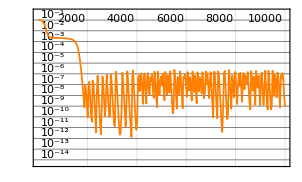
{NetChain[<>],NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:19s  examples/s:6059
data | ,,  training examples:11  processed examples:110000  skipped examples:0
method | ,,  ADAMoptimizer  batch size11CPU
round | ,,  loss:9.86×10^-10
 | rounds
loss | -Graphics- | 
 | ]}

```mathematica
secondnet = NetTrain[secondnet,traindata,{"TrainedNet", "ResultsObject"} ]
```

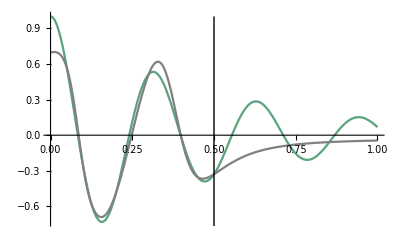

```mathematica
Show[
Plot[oscillator[2,20,x],{x,0,1}, ColorFunction->Hue],
Plot[secondnet[[1]][i], {i,0,1}, PlotStyle->Gray],
Graphics@Line[{{0.5, -1}, {0.5, 1}}]
]
```

```mathematica
HopefullyFinalNet = NetTrain[InitialNet,
 <|"xData"->xData,
 "Target"-> Targets
|>,
LossFunction->{"physloss", "loss1"},
MaxTrainingRounds->1000
]
```

NetGraph[<>]

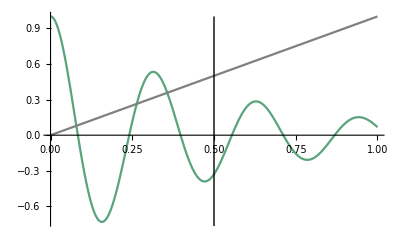

```mathematica
Show[
Plot[oscillator[2,20,x],{x,0,1}, ColorFunction->Hue],
Plot[HopefullyFinalNet[[1]][i], {i,0,1}, PlotStyle->Gray],
Graphics@Line[{{0.5, -1}, {0.5, 1}}]]
```